```mathematica
(* 1. naloga: Izračunajte prostornino telesa,ki ga dobimo,če zavrtimo krivuljo ___ na intervalu [0,pi] okrog x osi. Vnesite vrednost za prostornino na 5 decimalk natančno. *)
```

```mathematica
y=Sqrt[((8x+6)*Sin[x])/Pi]
V = N[Pi*Integrate[y^2,{x,0,Pi}],7]
```

(√((6+8 x) Sin[x]))/(√π)

37.13274

```mathematica
(* 2. naloga: Izračunajte konvergenčni polmer potenčne vrste ___) *)
Clear[a,n];
a[n_]:=n^6/9^n*x^n
R=Limit[Abs[a[n]/a[n+1]],n->Infinity] (* v rezultat dal 9*)
```

9/Abs[x]

-1/3+x/3

83/3-(32 x)/3+x^2

4.5

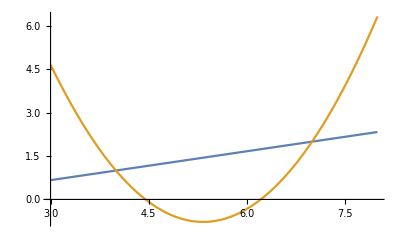

4.5

```mathematica
(* 3. naloga: Izračunajte ploščino območja med premico ___ in parabolo ___. Vnesite na 5 dec nazančno *)
y1=x/3-1/3
y2 = x^2-32x/3+83/3
nicle=Solve[x^2-32x/3+83/3==0,x];
xx=nicle[[All,1,2]];
xx[[1]];
xx[[2]];
SS=Integrate[y1,{x,4,7}]+Abs[Integrate[y2,{x,xx[[1]],xx[[2]]}]]-Integrate[y2,{x,4,xx[[1]]}]-Integrate[y2,{x,xx[[2]],7}]//N
Plot[{y1,y2},{x,3,8}]

(*zamaknemo za 1 navzdol*)
SS=Integrate[y1-1,{x,4,7}]+Abs[Integrate[y2-1,{x,4,20/3}]]-Integrate[y2-1,{x,20/3,7}]//N
```

```mathematica
(* 4. naloga: Določite vrednost funkcije ___ v stac. točki. Na 5 dec natančno *)
Clear[x,y,f];
f[x_,y_]=E^(3x)*(2x+y^2+3y)
(* Določitev stac. točk*)
fx=D[f[x,y],x] (*prvi odvod po x*)
fy=D[f[x,y],y] (*prvi odvod po y*)
sol=Solve[{fx==0,fy==0},{x,y}] 
stacionarna=E^(3x)*(2x+y^2+3y)/.sol//N
```

ⅇ^(3 x) (2 x+3 y+y^2)

2 ⅇ^(3 x)+3 ⅇ^(3 x) (2 x+3 y+y^2)

ⅇ^(3 x) (3+2 y)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→19/24,y→-3/2}}

{-7.16734}

```mathematica
(* 5. naloga: Izračunajte vrednost določenega integrala ___ na 5 decimalk. *)
Integrate[(1-2x)/((x-2)(x-1)),{x,3,6}]//N
```

-3.24259

```mathematica
(* 6. naloga: Izračunajte vrednost tretjega parcialnega odvoda fxyy funkcije ___ v točki T(1,-3). *)
Clear[x,y,f];
f=x^4+2x^3y+4x*y^3+y^4
fxyy=Simplify[D[f,x,y,y]]
vstavljenx=fxyy/.x->1
vstavljeny=vstavljenx/.y->-3
```

x^4+2 x^3 y+4 x y^3+y^4

24 y

24 y

-72

```mathematica
(* 7. naloga: Izračunajte vrednost določenega integrala ___ na 5 dec. natančno *)
```

```mathematica
N[Integrate[(E^(3x))/(E^(6x)+1),{x,0,Log[3]/6}],7]
```

0.08726646

ClearAll

(8 x^(3/2))/9

59/36

59/36-(3 x)/4

59/27

0.882305

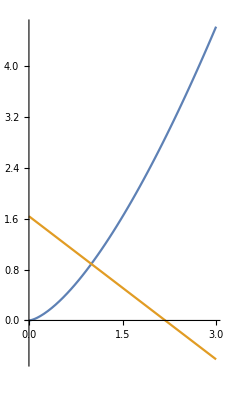

```mathematica
(* 8. naloga: Izračunajte ploščino lika,omejenega s krivuljo ___, normalo na to krivuljo v točki x0=1 in abscisno osjo. Na 5 dec natančno ploščino. *)
ClearAll
y=(8/9)*x^(3/2)
xn=1;
yn = y/.x->xn; (*damo v y x=1 da veš kok je vrednost v tej točki*)
kt=D[y,x]/.x->xn; (*odvod od funkcije y v 1 za smerni koef tangente.*)(* odvod je smerni koeficient tangente *)
kn = -1/kt; (* smerni koeficient normale*)
nn = yn-(kn*xn) (*seka y os*)
ynormale = kn*x+nn
b=x/.Flatten[Solve[ynormale==0,x]]
S=N[Integrate[y,{x,0,1}]+ Integrate[ynormale,{x,1,b}],6]
Plot[{y,ynormale},{x,0,3},AspectRatio->Automatic]
```

```mathematica
(* 9. naloga: Izračunajte dolžino loka krivulje ___ , 0<x<2. Vnesite vrednost za dolžino loka na 5 dec. *)
ClearAll
y=(8/9)*x^(3/2)
N[FullSimplify[Integrate[Sqrt[1+D[y,x]^2],{x,0,2}]]]
```

ClearAll

(8 x^(3/2))/9

3.27122

```mathematica
(* 10. Naloga: S pomočjo razvoja v Taylorjevo vrsto funkcije ___ do vključno potence x^3 izračunajte približno vrednost korena tretji koren iz 127. Rezultat na 5 dec natančno. *)
N[Table[Normal[Series[5(1+x)^(1/3),{x,0,n}]]/.x->2/125,{n,0,3}],7]
```

{5.,5.026667,5.026524,5.026526}